```mathematica
DateString[]
SetDirectory[NotebookDirectory[]]
```

Wed 11 Mar 2026 10:33:49

D:\titimbo\SingleSG_Xukun2025

```mathematica
dataExp = Transpose[{10^-3{0.0,11.620000000000001,15.32,19.98,25.53,32.7,41.87,52.9,67.5,85.88,109.2,142.3,179.1,229.6,292.90000000000003,374.0,479.0,613.0,695.0,782.0,890.0,944.0},
10^-4{21.921273974326578,76.68738542882397,94.96685685569611,116.74315632617501,148.26719260132444,187.96802228364228,236.46350596358872,308.33909740360616,409.66166180382794,532.2938436243059,688.2773513962201,939.2339196003039,1228.044308107841,1636.9497049810138,2152.0745381309894,2808.5711301481842,3649.623990396425,4670.618880949969,5260.813765536719,5828.916846178714,6451.293060726494,6725.169618954149}}];
```

```mathematica
data1 = Import["SG_BvsI.csv"];
data2 = Sort[Import["SG_BvsI_phywe.csv"],#1[[1]]<#2[[1]]&];
```

```mathematica
data2
```

{{-0.0351476,0.00519788},{-0.0313128,0.00519032},{-0.0281171,0.00518401},{-0.0249215,0.00517771},{-0.0217258,0.00517141},{-0.0191716,0.00388432},{-0.0153368,0.00387675},{-0.0127803,0.00387171},{-0.0102226,0.00450769},{-0.00702694,0.00450139},{-0.00383128,0.00449509},{3.51172×10^-6,0.00448752},{0.00383831,0.00447996},{0.0076731,0.0044724},{0.0115079,0.00446483},{0.0153427,0.00445727},{0.0191775,0.00444971},{0.0230123,0.00444214},{0.0268471,0.00443458},{0.0306819,0.00442701},{0.0351558,0.00441819},{0.0383515,0.00441189},{0.0415471,0.00440558},{0.0447428,0.00439928},{0.0479384,0.00439298},{0.0511341,0.00438667},{0.0543298,0.00438037},{0.0581646,0.00437281},{0.0607211,0.00436776},{0.0639168,0.00436146},{0.0677515,0.0043539},{0.0715863,0.00434633},{0.0754211,0.00433877},{0.0792559,0.00433121},{0.0830907,0.00432364},{0.0862864,0.00431734},{0.0901212,0.00430978},{0.093956,0.00430221},{0.0977908,0.00429465},{0.102265,0.00428582},{0.106099,0.00427826},{0.109295,0.00427196},{0.112493,0.0055477},{0.115694,0.00810549},{0.118289,0.0104125},{0.122127,0.0139384},{0.127457,0.0180249},{0.131908,0.020599},{0.138113,0.0247907},{0.142801,0.0278093},{0.14749,0.0307503},{0.151498,0.0339889},{0.156016,0.0368409},{0.160706,0.0404871},{0.165396,0.0440492},{0.170256,0.0476944},{0.174646,0.0506107},{0.179251,0.0544874},{0.185006,0.0583605},{0.189649,0.0620154},{0.194343,0.0656736},{0.199075,0.0689044},{0.204374,0.0729699},{0.208456,0.0766496},{0.213146,0.0805028},{0.217836,0.0844337},{0.222526,0.087946},{0.2273,0.0912645},{0.232758,0.0956422},{0.237447,0.0991073},{0.242137,0.10265},{0.24659,0.10598},{0.25109,0.109585},{0.255781,0.113413},{0.260471,0.117326},{0.265162,0.12147},{0.270023,0.125704},{0.274459,0.130104},{0.278916,0.134418},{0.283629,0.13917},{0.288191,0.142853},{0.292669,0.147287},{0.296911,0.151472},{0.301933,0.155498},{0.306529,0.159897},{0.31122,0.163983},{0.315697,0.167844},{0.320601,0.172214},{0.325079,0.176348},{0.329841,0.18032},{0.334674,0.185074},{0.336522,0.187157},{0.339366,0.18947},{0.341643,0.191634},{0.343843,0.19326},{0.346124,0.195472},{0.348427,0.197333},{0.351886,0.200588},{0.353807,0.202508},{0.356211,0.204722},{0.358928,0.206985},{0.361115,0.209167},{0.36405,0.212103},{0.36666,0.214765},{0.371137,0.218734},{0.376468,0.223515},{0.380732,0.227246},{0.384713,0.231318},{0.389774,0.236019},{0.394427,0.240124},{0.398643,0.243233},{0.404185,0.247493},{0.408876,0.251773},{0.413195,0.25617},{0.417218,0.260701},{0.421331,0.264652},{0.425938,0.269354},{0.430202,0.273004},{0.434893,0.276987},{0.439541,0.280949},{0.443787,0.284781},{0.447924,0.289057},{0.452378,0.293456},{0.45707,0.298286},{0.460644,0.302754},{0.465604,0.308411},{0.469444,0.313013},{0.473649,0.317642},{0.477549,0.321647},{0.48224,0.326076},{0.486931,0.330169},{0.491195,0.333842},{0.496865,0.338247},{0.501109,0.342128},{0.505056,0.347112},{0.509345,0.351448},{0.514142,0.356531},{0.518875,0.360906},{0.523609,0.365176},{0.527288,0.368969},{0.532352,0.373477},{0.536404,0.377544},{0.541096,0.382642},{0.545363,0.387617},{0.550056,0.392795},{0.554791,0.398191},{0.559313,0.403114},{0.563708,0.408291},{0.567888,0.412383},{0.572997,0.417714},{0.576078,0.420972},{0.577968,0.42375},{0.581836,0.42679},{0.586314,0.431154},{0.590792,0.435205},{0.59527,0.439443},{0.599994,0.444024},{0.604286,0.447483},{0.608773,0.45114},{0.613653,0.454926},{0.618295,0.458723},{0.622986,0.462764},{0.626827,0.467745},{0.631517,0.47163},{0.635568,0.475293},{0.639621,0.479747},{0.644617,0.484701},{0.648322,0.488532},{0.651869,0.492291},{0.658215,0.496732},{0.662521,0.500481},{0.667802,0.505324},{0.672635,0.509567},{0.677321,0.514913},{0.68163,0.519531},{0.68677,0.523846},{0.690637,0.527074},{0.695147,0.53099},{0.699712,0.534343},{0.704762,0.53878},{0.710081,0.543743},{0.714676,0.547482},{0.718856,0.551739},{0.723634,0.556714},{0.72902,0.562734},{0.733587,0.567205},{0.738137,0.572314},{0.741881,0.575895},{0.746615,0.580945},{0.751787,0.58627},{0.755946,0.590747},{0.760745,0.595737},{0.765057,0.599596},{0.7697,0.603555},{0.774219,0.606927},{0.779165,0.611219},{0.784007,0.615144},{0.788248,0.618855},{0.79214,0.622728},{0.796565,0.627414},{0.800946,0.631353},{0.806202,0.635687},{0.811106,0.639862},{0.815814,0.643342},{0.82087,0.647824},{0.82556,0.651677},{0.830252,0.656085},{0.834896,0.660923},{0.839591,0.664721},{0.844324,0.668336},{0.849014,0.672172},{0.85541,0.677756},{0.859865,0.682058},{0.864792,0.686385},{0.869482,0.689632},{0.874171,0.69302},{0.878434,0.695899},{0.883976,0.700065},{0.888538,0.703931},{0.893356,0.707655},{0.898217,0.711555},{0.90231,0.715067},{0.906573,0.717625},{0.911433,0.721222},{0.915951,0.724361},{0.92064,0.72738},{0.925371,0.730482},{0.930498,0.734331},{0.934708,0.737425},{0.939397,0.74051},{0.944084,0.742745},{0.949042,0.744885},{0.953886,0.748231},{0.958575,0.751023},{0.963262,0.75346},{0.967948,0.7551},{0.972635,0.757148},{0.976968,0.759459},{0.98201,0.761807},{0.986698,0.76436},{0.991216,0.766775},{0.995587,0.769106},{1.00076,0.77163},{1.00575,0.774091},{1.01056,0.776327},{1.01525,0.778246},{1.0197,0.780405},{1.02466,0.781967},{1.02931,0.784365},{1.034,0.786626},{1.03868,0.788597},{1.04337,0.790043},{1.04806,0.791936},{1.0527,0.793534},{1.05743,0.795314},{1.06197,0.796595},{1.06606,0.798088},{1.07149,0.799396},{1.07698,0.800546},{1.08175,0.802031},{1.08639,0.803021},{1.09108,0.804565},{1.09577,0.805953},{1.10045,0.807787},{1.10482,0.80922},{1.10959,0.81064},{1.11427,0.811698},{1.1198,0.813138},{1.12402,0.814739},{1.12857,0.815942},{1.13292,0.816999},{1.13794,0.818253},{1.14262,0.819505},{1.14754,0.821074},{1.15166,0.821967},{1.15659,0.823134},{1.1616,0.824462},{1.16605,0.825728},{1.17073,0.826689},{1.17542,0.828097},{1.18059,0.829651},{1.18479,0.830466},{1.18933,0.831477},{1.19408,0.832583},{1.19927,0.833232},{1.20438,0.834445},{1.21034,0.834869},{1.21593,0.836383},{1.22035,0.837271},{1.22568,0.838343},{1.23036,0.839751},{1.23505,0.840809},{1.23925,0.841644},{1.24429,0.842838},{1.2491,0.843576},{1.25383,0.844741},{1.25847,0.84579},{1.26297,0.846657},{1.26827,0.847692},{1.27295,0.848595},{1.27764,0.849614},{1.28232,0.850919},{1.28701,0.851692},{1.29169,0.852226},{1.29657,0.852877},{1.30149,0.853973},{1.30617,0.854508},{1.31166,0.855338},{1.31611,0.855637},{1.32108,0.856303},{1.32576,0.85674},{1.33044,0.857119},{1.33492,0.857178},{1.34024,0.857235}}

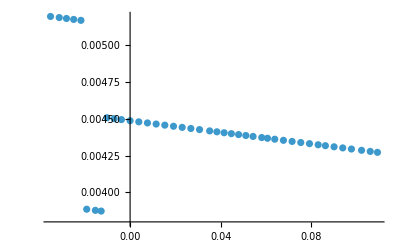

```mathematica
ListPlot[data2[[;;42,;;]],PlotRange->All]
```

FittedModel[…]

0.0044482

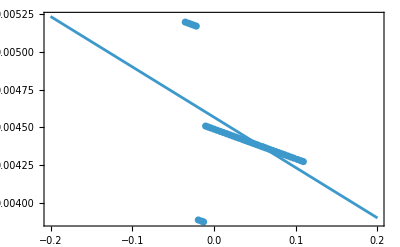

FittedModel[…]

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 0.0044482 | 0.0000479816 | 92.7064 | 2.89795×10^-49,0.995252,0.995136}

```mathematica
datafit1=data2[[;;42,;;]];
lf1=LinearModelFit[datafit1,x,x]
Mean[datafit1[[;;,2]]]
Show[ListPlot[datafit1],Plot[lf1[x],{x,-0.2,0.2}],Frame->True,PlotRange->All]
nlm1=NonlinearModelFit[datafit1,a,a,x]
nlm1[{"ParameterTable","RSquared","AdjustedRSquared"}]
```

FittedModel[…]

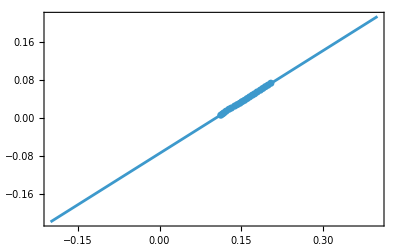

{ | Estimate | Standard Error | t-Statistic | P-Value
a | -0.0752333 | 0.000608687 | -123.599 | 4.48559×10^-29
b | 0.722926 | 0.00382689 | 188.907 | 1.42631×10^-32,0.999879,0.999867}

```mathematica
datafit2=data2[[43;;63,;;]];
lf2=LinearModelFit[datafit2,x,x]
Show[ListPlot[datafit2],Plot[lf2[x],{x,-0.2,0.4}],Frame->True,PlotRange->All]
nlm2=NonlinearModelFit[datafit2,a+b x,{a,b},x];
nlm2[{"ParameterTable","RSquared","AdjustedRSquared"}]
```

```mathematica
Icutting = Solve[Normal[nlm2]==Normal[nlm1],x][[1,1,2]]
```

0.110221

```mathematica
data3 = Transpose[{data2[[;;,1]]-Icutting,data2[[;;,2]]-Normal[nlm1]}];
data3a = Transpose[{data2[[;;,1]]-Icutting,data2[[;;,2]]}];
```

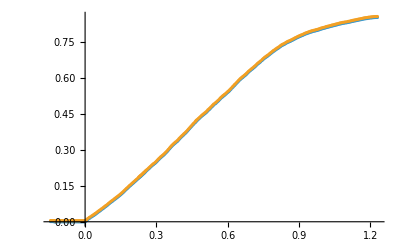

```mathematica
ListPlot[{data3,data3a}]
```

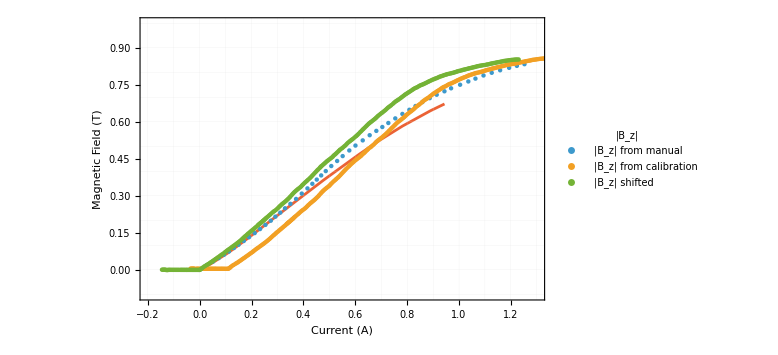

```mathematica
ListPlot[{data1,data2,data3,dataExp},
Frame->True,
Joined->{False,False,False,True},
PlotRange->{{-0.2,1.3},{-0.1,1.0}},
FrameLabel->{Style["Current (A)",Bold,12],Style[ "Magnetic Field (T)",Bold,12]},
LabelStyle->Directive[10],
GridLines->All,
GridLinesStyle->Directive[LightGray,Thickness[0.0001]],
PlotLegends->Placed[PointLegend[
{Style["|B_z| from manual",8],
Style["|B_z| from calibration",8],
Style["|B_z| shifted",8]},
LegendFunction->(Framed[#,RoundingRadius->5,Background->White]&),
LegendMargins->1,
Spacings->0.05,
LegendLabel->"|B_z|"],{Right,Bottom}],
ImageSize->Large]
```

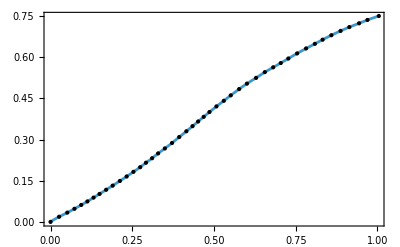

```mathematica
ifun1 = Interpolation[data1,InterpolationOrder->5];
Plot[ifun1[x],{x,0,1},Epilog->Point[data1],Frame->True]
```

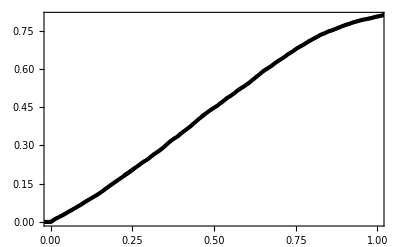

```mathematica
ifun3 = Interpolation[data3,InterpolationOrder->5];
Plot[ifun3[x],{x,0,1},Epilog->Point[data3],Frame->True]
```

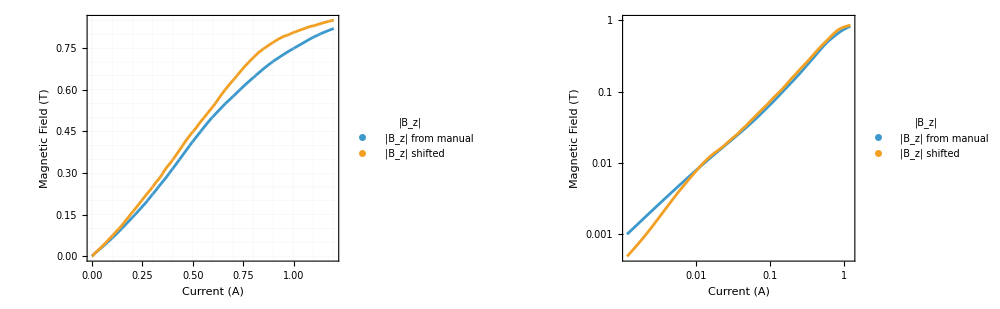

```mathematica
GraphicsRow[{
Plot[{ifun1[x],ifun3[x]},{x,0,1.2},
Frame->True,
FrameLabel->{Style["Current (A)",Bold,12],Style[ "Magnetic Field (T)",Bold,12]},
LabelStyle->Directive[10],
GridLines->All,
GridLinesStyle->Directive[LightGray,Thickness[0.0001]],
PlotLegends->Placed[PointLegend[
{Style["|B_z| from manual",8],
Style["|B_z| shifted",8]},
LegendFunction->(Framed[#,RoundingRadius->5,Background->White]&),
LegendMargins->1,
Spacings->0.05,
LegendLabel->"|B_z|"],{Right,Bottom}],
ImageSize->Large],
LogLogPlot[{ifun1[x],ifun3[x]},{x,0,1.2},
Frame->True,
FrameLabel->{Style["Current (A)",Bold,12],Style[ "Magnetic Field (T)",Bold,12]},
LabelStyle->Directive[10],
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Thickness[0.0001]],
PlotLegends->Placed[PointLegend[
{Style["|B_z| from manual",8],
Style["|B_z| shifted",8]},
LegendFunction->(Framed[#,RoundingRadius->5,Background->White]&),
LegendMargins->1,
Spacings->0.05,
LegendLabel->"|B_z|"],{Right,Bottom}],
ImageSize->Large]
},ImageSize->1000]
```

```mathematica
(51.778*6.5)/(2 √(2Log[2]))
```

142.923